# Diaphorina Network Model

## Single System Model

### Auxiliary Functions

```mathematica
ChartReport[init_,param1_,param2_,param3_,param4_]:=Transpose@Dataset[List@@@Normal[Dataset/@Association[
{"init"->Association@Thread[{"x1[0]","x2[0]","x3[0]","x4[0]","t"}->init]},
{"x1"->Association@Thread[{"r1","b12","b13","a1","c1"}->param1]},{"x2"->Association@Thread[{"r2","b21","b24","a2","c2"}->param2]},{"x3"->Association@Thread[{"r3","b31","a3","c3"}->param3]},{"x4"->Association@Thread[{"r4","b42","a4","c4"}->param4]}]]]
```

### System Equations

```mathematica
ClearAll[SystemEvolve];
Options[SystemEvolve]={"LabelPosition"->{0.88,0.85}};
SystemEvolve[δ_,T_,{{r1_,b12_,b13_,a1_,c1_},{r2_,b21_,b24_,a2_,c2_},{r3_,b31_,a3_,c3_},{r4_,b42_,a4_,c4_}},{Di0_,B0_,x30_,x40_,tt_},opts:OptionsPattern[]]:=Module[
{x,eqs,x1,x2,x3,x4},
eqs=NDSolve[{
(x1'[t]==x1[t]*(r1+b12*x2[t]+b13*x3[t]-(a1+c1*(b12*x2[t]+b13*x3[t]))*x1[t])), (*Diaphorina citri*)
(x2'[t]==x2[t]*(r2+b21*x1[t]+b24*x4[t]-(a2+c2*(b21*x1[t]+b24*x4[t]))*x2[t])), (*Plant shoots*)
(x3'[t]==x3[t]*(r3+b31*x1[t]-(a3+c3*b31*x1[t])*x3[t])), (*Tamarixia radiata*)
(x4'[t]==x4[t]*(r4+b42*x2[t]-(a4+c4*b42*x2[t])*x4[t])), (*Stimuli*)
x1[0]==Di0,
x2[0]==B0,
x3[0]==x30,
x4[0]==x40,
WhenEvent[Mod[t,T]==0 && t>0, x3[t]->x3[t]+δ]
},
{x1,x2,x3,x4},{t,0,tt},Method->{"TimeIntegration"->"ExplicitRungeKutta"}];
Plot[Evaluate[{x1[t],x2[t],x3[t],x4[t]}/.eqs],{t,0,tt},
	PlotLegends->Placed[{"Diaphorina citri","Plant shoots","Tamarixia radiata","Stimuli"},OptionValue["LabelPosition"]],
	PlotRange->All, FrameLabel->{"time (a.u.)", "population"},GridLines->Automatic,GridLinesStyle->Directive[Dashed],Frame->True,ImageSize->Large]
]
```

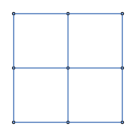

```mathematica
g=GridGraph[{3,3}]
```

```mathematica
L=Normal@KirchhoffMatrix[g];
L//MatrixForm
```

(2 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0
-1 | 3 | -1 | 0 | -1 | 0 | 0 | 0 | 0
0 | -1 | 2 | 0 | 0 | -1 | 0 | 0 | 0
-1 | 0 | 0 | 3 | -1 | 0 | -1 | 0 | 0
0 | -1 | 0 | -1 | 4 | -1 | 0 | -1 | 0
0 | 0 | -1 | 0 | -1 | 3 | 0 | 0 | -1
0 | 0 | 0 | -1 | 0 | 0 | 2 | -1 | 0
0 | 0 | 0 | 0 | -1 | 0 | -1 | 3 | -1
0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 2)

```mathematica
n=VertexCount[g]
```

9

```mathematica
NDSolve[{
(x1'[t]==x1[t]*(r1+b12*x2[t]+b13*x3[t]-(a1+c1*(b12*x2[t]+b13*x3[t]))*x1[t])), (*Diaphorina citri*)
(x2'[t]==x2[t]*(r2+b21*x1[t]+b24*x4[t]-(a2+c2*(b21*x1[t]+b24*x4[t]))*x2[t])), (*Plant shoots*)
(x3'[t]==x3[t]*(r3+b31*x1[t]-(a3+c3*b31*x1[t])*x3[t])), (*Tamarixia radiata*)
(x4'[t]==x4[t]*(r4+b42*x2[t]-(a4+c4*b42*x2[t])*x4[t])), (*Stimuli*)
x1[0]==Di0,
x2[0]==B0,
x3[0]==x30,
x4[0]==x40,
WhenEvent[Mod[t,T]==0 && t>0, x3[t]->x3[t]+δ]
},
{x1,x2,x3,x4},{t,0,tt},Method->{"TimeIntegration"->"ExplicitRungeKutta"}]
```